```mathematica
v[r_]:=√(2/r)
ccc=2.998 10^10;
κes=0.34 9.118 10^21;
kbt=9.184 10^-14;
kbme=1.6861708837290192 10^-10;
Rg[Mbh_]:=147700Mbh
Tgas[r_]:=3.267 10^12/r
LumEdd=(4π)/κes;
LumEddcgs[Mbh_]:=1.25 10^38 Mbh
MdotEddcgs[Mbh_]:=LumEddcgs[Mbh]/ccc^2
ρcgs[r_,Mdot_,Mbh_]:=(Mdot MdotEddcgs[Mbh])/(4π (r Rg[Mbh])^2(v[r]ccc))
ρ[r_,Mdot_,Mbh_]:=ρcgs[r,Mdot,Mbh]/(6.17 10^15)
u[r_,Mdot_,Mbh_]:=1/(5/3-1)9.18 10^-14 Tgas[r]ρ[r,Mdot,Mbh]
Ehat[r_,lum_]:=lum LumEdd/(4π r^2)

Rtrap[Mdot_]:=Mdot;
mpcgs=1.67 10^-24;
ϵff[ρ_,T_]:=1.4 10^-27 T^(1/2)(ρ/mpcgs)^2
Lumcgs[Mdot_,Mbh_]:=∫_(Rtrap[Mdot]Rg[Mbh])^Infinity 4π r^2 ϵff[ρcgs[r/Rg[Mbh],Mdot,Mbh],Tgas[r/Rg[Mbh]]]ⅆr
```

```mathematica
u[10^5,100,10]
```

2.75884×10^-33

```mathematica
Ehat[10^5,.1]
```

3.22568×10^-33

```mathematica
(* fractional change of internal energy density by the Comptonization assuming Ehat = ugas *)
fraction[r_,Mdot_,Trad_,Mbh_]:=Abs[r/v[r] κes ρ[r,Mdot,Mbh]4kbme(Tgas[r]-Trad)]
(* fractional change of internal energy density by the Comptonization not assuming Ehat = ugas *)fraction2[r_,Mdot_,Trad_,Mbh_,lum_]:=Abs[Ehat[r,lum]/u[r,Mdot,Mbh] r/v[r] κes ρ[r,Mdot,Mbh]4kbme(Tgas[r]-Trad)]
```

```mathematica
test[r_,Mdot_,Trad_,Mbh_,lum_]:=Ehat[r,lum]/(1+u[r,Mdot,Mbh])
```

```mathematica
Plot[{-2 Rb-30,Log10[test[10^Rb,10^0,10^9.5,10,10^-1]]},{Rb,4,6}];
```

```mathematica
Plot[{1lum,Log10[fraction2[10^5,10^0,10^9.5,10,10^lum]]},{lum,-2,4}];
```

```mathematica
Manipulate[ContourPlot[Log10[fraction2[10^R,10^1,10^Trad,10,10^lum]],{lum,-4,2},{Trad,4,13},ContourLabels->All,FrameLabel->{"log(lum)","log(Trad)",R}
],{R,5,5}]
```

```mathematica
Manipulate[ContourPlot[Log10[fraction[10^R,10^Mdot,10^Trad,10]],{Mdot,-2,5},{Trad,4,11},ContourLabels->All,FrameLabel->{"log(Mdot)","log(Trad)",R}
],{R,1,9}]
```

```mathematica
lum[Mdot_]:=Lumcgs[Mdot,100]/LumEddcgs[100]
```

```mathematica
lum[1000]
```

2.67286

Integrate::idiv: Integral of (1/r)^3/2 does not converge on {-6.80128×10^7, ∞}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {-1.48686×10^7}. NIntegrate obtained 3.02356×10^37 - 7.01755×10^38\ ⅈ and 6.77035×10^38 for the integral and error estimates.

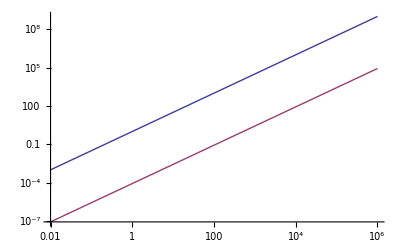

```mathematica
LogLogPlot[{Mdot^1.5,lum[Mdot]},{Mdot,10^-2,10^6}]
```

```mathematica
`
```

```mathematica
Rg[10]
```

1477000